```mathematica
Distance[n_, p_] := Module[ {threshold, digits, position, found, nextPower, result},
  If [n == 0, Return[0]];
  (* Initialize some precomputed local varables *)
  threshold = (p - 1)/2;
  digits = IntegerDigits[n, p];
  
  (* find the first digit above the threshold *)
  found = -1;
  For[ position = 1, position <= Length[digits], position++,
   If [ digits [[position]] > threshold,
    found = position; Break[]
    ]
   ];
  
  (* if we didn't find a digit, then the distance is zero *)
  If [found == -1, Return[0]];
  
  (* we did find a faulty digit.  Now we need to look before it for digits that equal the threshold.
  If we would not count these then we would end up with a new value which is still not p-good (due
  to the carrying) *)
  While[ found > 1,
   If [ digits [[found - 1]] == threshold, found --, Break[]]
   ];
  
  (* if we have gone all the way to the start*)
  If[found == 1,
   Block[{},
    nextPower = p^(Length[digits]);
    Return[nextPower - n]
    ]
   ];
  
  
  nextPower = p^(Length[digits] + 1 - found);
  Return[nextPower - FromDigits[Take[digits, -(Length[digits] + 1 - found)], p]]
  ]
```

```mathematica
AlgoList4[start_, end_, primes_] := AlgoList4[start, end, primes]=Module[{result, current,  maxdist, hops,distances},
result = 0;
current=start;
hops=0;
Monitor[
While[current ≤ end,
(*Print[current];*)
hops++;
distances=ParallelTable[Distance[current, p], {p, primes}];
maxdist = Max[distances];
If[maxdist==0,
result+=1;
current +=Max[Min[ParallelTable[Distance[current+1, p], {p, primes}]],1];
,
current += maxdist;
];
],
{primes,hops, result,N[Log[10,current]]}
];

PrintTemporary [{primes,result,hops}];
Return [{primes,result,hops}];
]
```

```mathematica
values=With[
{step=1, base=10},
Table[
With[
{a=Timing[{exp,exp+step,AlgoList4[base^exp,base^(exp+step),{3,5,7}]}]},
Print[a];Last[Last[Last[a]]]],
{exp,0,200,step}
]
]
```

{7.49623×10^-13,{0,1,{{3,5,7},2,6}}}

{7.49623×10^-13,{1,2,{{3,5,7},1,6}}}

{7.49623×10^-13,{2,3,{{3,5,7},2,15}}}

{7.49623×10^-13,{3,4,{{3,5,7},7,34}}}

{7.49623×10^-13,{4,5,{{3,5,7},1,29}}}

{7.49623×10^-13,{5,6,{{3,5,7},0,6}}}

{7.49623×10^-13,{6,7,{{3,5,7},0,7}}}

{7.49623×10^-13,{7,8,{{3,5,7},2,67}}}

{7.49623×10^-13,{8,9,{{3,5,7},0,7}}}

{7.49623×10^-13,{9,10,{{3,5,7},0,4}}}

{7.49623×10^-13,{10,11,{{3,5,7},2,128}}}

{7.49623×10^-13,{11,12,{{3,5,7},0,31}}}

{7.49623×10^-13,{12,13,{{3,5,7},0,7}}}

{7.49623×10^-13,{13,14,{{3,5,7},0,11}}}

{7.49623×10^-13,{14,15,{{3,5,7},1,83}}}

{7.49623×10^-13,{15,16,{{3,5,7},0,7}}}

{7.49623×10^-13,{16,17,{{3,5,7},25,317}}}

{7.49623×10^-13,{17,18,{{3,5,7},19,241}}}

{7.49623×10^-13,{18,19,{{3,5,7},0,22}}}

{7.49623×10^-13,{19,20,{{3,5,7},0,12}}}

{7.49623×10^-13,{20,21,{{3,5,7},0,25}}}

{7.49623×10^-13,{21,22,{{3,5,7},3,106}}}

{7.49623×10^-13,{22,23,{{3,5,7},0,22}}}

{7.49623×10^-13,{23,24,{{3,5,7},0,6}}}

{7.49623×10^-13,{24,25,{{3,5,7},16,246}}}

{7.49623×10^-13,{25,26,{{3,5,7},0,10}}}

{7.49623×10^-13,{26,27,{{3,5,7},48,779}}}

{7.49623×10^-13,{27,28,{{3,5,7},0,25}}}

{7.49623×10^-13,{28,29,{{3,5,7},6,275}}}

{7.49623×10^-13,{29,30,{{3,5,7},0,34}}}

{7.49623×10^-13,{30,31,{{3,5,7},29,690}}}

{7.49623×10^-13,{31,32,{{3,5,7},4,253}}}

{7.49623×10^-13,{32,33,{{3,5,7},8,707}}}

{7.49623×10^-13,{33,34,{{3,5,7},0,13}}}

{7.49623×10^-13,{34,35,{{3,5,7},0,108}}}

{7.49623×10^-13,{35,36,{{3,5,7},0,35}}}

{7.49623×10^-13,{36,37,{{3,5,7},0,9}}}

{7.49623×10^-13,{37,38,{{3,5,7},0,21}}}

{7.49623×10^-13,{38,39,{{3,5,7},0,5}}}

{7.49623×10^-13,{39,40,{{3,5,7},0,16}}}

{7.49623×10^-13,{40,41,{{3,5,7},0,28}}}

{7.49623×10^-13,{41,42,{{3,5,7},0,10}}}

{7.49623×10^-13,{42,43,{{3,5,7},0,6}}}

{7.49623×10^-13,{43,44,{{3,5,7},119,3805}}}

{7.49623×10^-13,{44,45,{{3,5,7},5,839}}}

{7.49623×10^-13,{45,46,{{3,5,7},0,8}}}

{7.49623×10^-13,{46,47,{{3,5,7},0,7}}}

{7.49623×10^-13,{47,48,{{3,5,7},0,32}}}

{7.49623×10^-13,{48,49,{{3,5,7},58,1731}}}

{7.49623×10^-13,{49,50,{{3,5,7},0,83}}}

{7.49623×10^-13,{50,51,{{3,5,7},0,69}}}

{7.49623×10^-13,{51,52,{{3,5,7},0,20}}}

{7.49623×10^-13,{52,53,{{3,5,7},48,1858}}}

{7.49623×10^-13,{53,54,{{3,5,7},0,5}}}

{7.49623×10^-13,{54,55,{{3,5,7},0,8}}}

{7.49623×10^-13,{55,56,{{3,5,7},0,14}}}

{7.49623×10^-13,{56,57,{{3,5,7},293,8466}}}

{7.49623×10^-13,{57,58,{{3,5,7},0,4}}}

{7.49623×10^-13,{58,59,{{3,5,7},0,30}}}

{7.49623×10^-13,{59,60,{{3,5,7},0,5}}}

{7.49623×10^-13,{60,61,{{3,5,7},0,497}}}

{7.49623×10^-13,{61,62,{{3,5,7},0,9}}}

{7.49623×10^-13,{62,63,{{3,5,7},0,15}}}

{7.49623×10^-13,{63,64,{{3,5,7},0,9}}}

{7.49623×10^-13,{64,65,{{3,5,7},0,6}}}

{7.49623×10^-13,{65,66,{{3,5,7},675,17059}}}

{7.49623×10^-13,{66,67,{{3,5,7},0,10}}}

{7.49623×10^-13,{67,68,{{3,5,7},0,12}}}

{7.49623×10^-13,{68,69,{{3,5,7},0,16}}}

{7.49623×10^-13,{69,70,{{3,5,7},0,77}}}

{7.49623×10^-13,{70,71,{{3,5,7},272,9156}}}

{7.49623×10^-13,{71,72,{{3,5,7},0,4}}}

{7.49623×10^-13,{72,73,{{3,5,7},0,28}}}

{7.49623×10^-13,{73,74,{{3,5,7},474,18310}}}

{7.49623×10^-13,{74,75,{{3,5,7},2653,88548}}}

{7.49623×10^-13,{75,76,{{3,5,7},0,27}}}

{7.49623×10^-13,{76,77,{{3,5,7},61,2764}}}

{7.49623×10^-13,{77,78,{{3,5,7},0,9}}}

{7.49623×10^-13,{78,79,{{3,5,7},0,6}}}

{7.49623×10^-13,{79,80,{{3,5,7},0,10}}}

{7.49623×10^-13,{80,81,{{3,5,7},0,44}}}

{7.49623×10^-13,{81,82,{{3,5,7},2749,97449}}}

{7.49623×10^-13,{82,83,{{3,5,7},588,17743}}}

{7.49623×10^-13,{83,84,{{3,5,7},1057,38232}}}

{7.49623×10^-13,{84,85,{{3,5,7},773,22401}}}

{7.49623×10^-13,{85,86,{{3,5,7},0,90}}}

{7.49623×10^-13,{86,87,{{3,5,7},73,4191}}}

{7.49623×10^-13,{87,88,{{3,5,7},0,13}}}

{7.49623×10^-13,{88,89,{{3,5,7},141,6171}}}

{7.49623×10^-13,{89,90,{{3,5,7},0,6}}}

{7.49623×10^-13,{90,91,{{3,5,7},0,5}}}

{7.49623×10^-13,{91,92,{{3,5,7},0,85}}}

{7.49623×10^-13,{92,93,{{3,5,7},0,47}}}

{7.49623×10^-13,{93,94,{{3,5,7},0,14}}}

{7.49623×10^-13,{94,95,{{3,5,7},0,5}}}

{7.49623×10^-13,{95,96,{{3,5,7},0,8}}}

{7.49623×10^-13,{96,97,{{3,5,7},0,9}}}

{7.49623×10^-13,{97,98,{{3,5,7},0,10}}}

{7.49623×10^-13,{98,99,{{3,5,7},0,145}}}

{7.49623×10^-13,{99,100,{{3,5,7},4059,149211}}}

{7.49623×10^-13,{100,101,{{3,5,7},2768,98321}}}

{7.49623×10^-13,{101,102,{{3,5,7},0,6}}}

{7.49623×10^-13,{102,103,{{3,5,7},0,79}}}

{7.49623×10^-13,{103,104,{{3,5,7},0,16}}}

{7.49623×10^-13,{104,105,{{3,5,7},0,10}}}

{7.49623×10^-13,{105,106,{{3,5,7},0,87}}}

{7.49623×10^-13,{106,107,{{3,5,7},0,15}}}

{7.49623×10^-13,{107,108,{{3,5,7},0,8}}}

{7.49623×10^-13,{108,109,{{3,5,7},0,7}}}

{7.49623×10^-13,{109,110,{{3,5,7},7089,239230}}}

{7.49623×10^-13,{110,111,{{3,5,7},0,253}}}

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable will be suppressed during this calculation.

{0.032,{111,112,{{3,5,7},0,32}}}

{1.50635×10^-12,{112,113,{{3,5,7},0,7}}}

{583.521,{113,114,{{3,5,7},7077,250377}}}

{0.016,{114,115,{{3,5,7},0,22}}}

{0.016,{115,116,{{3,5,7},0,8}}}

{1523.83,{116,117,{{3,5,7},18134,656092}}}

{2750.53,{117,118,{{3,5,7},31904,1110186}}}

$Aborted

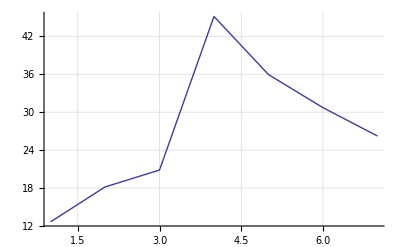

```mathematica
ListPlot[{177/14,854/47,1522/73,1851/41,6543/182,10474/341,17704/675},Joined->True,GridLines->Automatic]
```

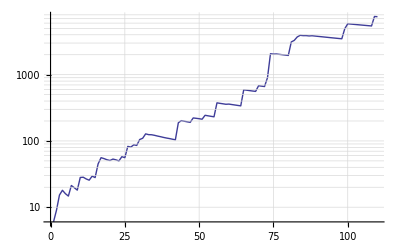

```mathematica
ListLogPlot[Table[Mean[Take[values,i]],{i,2,Length[values]}],Joined->True,GridLines->Automatic]
```

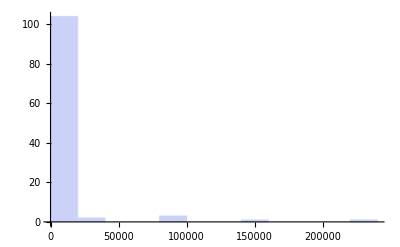

```mathematica
Histogram[values]
```